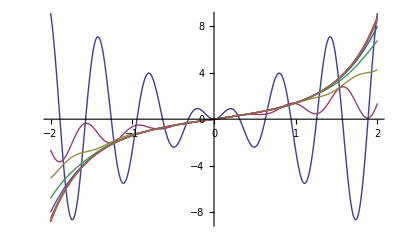

Погрешность приближения равна: 0.0880728

```mathematica
(*Зададим правую часть ДУ*)
f[x_,y_]=x*y+1;
(*Зададим начальное условие*)
x0=0;
y0=0;
(*Зададим количество итераций метода Пикара*)
n=5;
(*Зададим начальное приближение к решению*)
Y={5*x*Sin[10*x]};
(*Реализуем алгоритм метода Пикара*)
For[k=1,k≤n+1,k++,
AppendTo[Y,y0+Integrate[f[x,Y[[k]]],{x,x0,x}]]
];
(*Найдем точное решение задачи Коши*)
DSol=DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x];
sol[x_]=y[x]/.DSol[[1]];
(*Построим график точного решения и последовательности приближений в одной системе координат*)
G=Plot[sol[x],{x,x0-2,x0+2},PlotStyle->Red];
GY=Plot[Y,{x,x0-2,x0+2}];
Show[G,GY]
r=NIntegrate[Abs[Y[[n+1]]-sol[x]],{x,x0-2,x0+2}];
Print["Погрешность приближения равна: ",r]
```

```mathematica
(*Выполним анимацию последовательности приближений к точному решению*)
Animate[Show[G,Plot[Y[[k]],{x,x0-2,x0+2}]],{k,1,n+1,1},AnimationRunning->False]
```